# SpinDynamica Optimal Control Tutorial 01: Single-Spin GRAPE Foundations

## Constructing OptimalControlProblem tasks, running GRAPEOptimize, verifying gradients and propagators, applying RF constraints and smooth bases, and exporting waveforms.

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that all OptimalControl` packages loaded cleanly.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator, Duration, Exp, Expand, Plus, Power, Simplify, SolidAngle, Times, WignerD}

```mathematica
{Select[$Packages,StringStartsQ[#,"OptimalControl`"]&],Context[OptimalControlProblem],Context[GRAPEOptimize]}
```

{{OptimalControl`Visualization`,OptimalControl`TimeOptimal`,OptimalControl`SecondOrderOptimizers`,OptimalControl`Optimizers`,OptimalControl`Ensemble`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`},OptimalControl`GRAPE`,OptimalControl`GRAPE`}

## 1. Defining an OptimalControlProblem

An optimal-control task in SpinDynamica is defined by four ingredients:
  1. A drift Hamiltonian H0 (static or time-dependent),
  2. A list of control Hamiltonians {H1, H2, ...},
  3. A target specification (state, observable, coherence, or unitary gate),
  4. A timing specification ({totalDuration, nSlices}, scalar totalDuration with TimeSteps -> n, or an explicit list of slice durations).

Here we define a single liquid-state spin-1/2 with a 150 Hz chemical-shift offset and two orthogonal RF control channels {Ix, Iy}. FrequencyUnits defaults to "rad/s", while ControlUnits -> "Hz" lets us enter and read RF amplitudes directly in Hz.

```mathematica
SetSpinSystem[{{1,1/2}}];
H0=2.*Pi*150.*opI[1,"z"];
ctrls={opI[1,"x"],opI[1,"y"]};
targetInv=ObservableTarget[opI[1,"z"]->-opI[1,"z"]];
probInv=OptimalControlProblem[H0,ctrls,targetInv,{0.002,40},FrequencyUnits->"rad/s",ControlUnits->"Hz"]
```

1
SetSpinSystem::set : the spin system has been set to {{1, -}}
                                                          2

1
SetBasis::set : the state basis has been set to ZeemanBasis[{{1, -}}, BasisLabels -> Automatic].
                                                                 2

OptimalControlProblem[942.478 I_(1z),{I_(1x),I_(1y)},ObservableTarget[I_(1z)→-I_(1z)],{0.002,40},FrequencyUnits→rad/s,ControlUnits→Hz]

Throughout this notebook we keep this same spin-1/2 system and 2 ms timing grid so each section isolates only the new options being introduced.

## 2. Your First GRAPEOptimize Run

Pass the OptimalControlProblem (or its positional arguments directly) to GRAPEOptimize (alias OptimalControlOptimize). Setting RandomSeed makes the initial random guess reproducible, and TargetFidelity -> 0.9999 stops early once fidelity exceeds 99.99%.

```mathematica
resInv=GRAPEOptimize[probInv,RandomSeed->42,TargetFidelity->0.9999]
```

OptimalControlResult[…]

SpinDynamica provides dedicated visualizers for optimal-control results: PlotOptimalControlWaveform (either "Cartesian" ux/uy or polar "AmplitudePhase"), PlotOptimalControlConvergence ("Infidelity" on a log scale), and PlotOptimalControlTrajectory for expectation values of spin observables along the pulse.

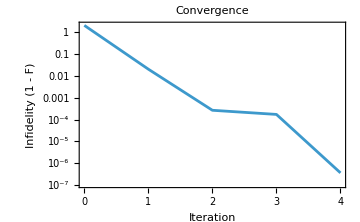

```mathematica
GraphicsRow[{PlotOptimalControlWaveform[resInv,Method->"Cartesian",PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"Optimized RF (Cartesian)"],PlotOptimalControlConvergence[resInv,Method->"Infidelity",PlotLabel->"Convergence"]},ImageSize->760,Spacings->25]
```

```mathematica
GraphicsRow[{PlotOptimalControlWaveform[resInv,Method->"AmplitudePhase"],PlotOptimalControlTrajectory[resInv,opI[1,"z"],{opI[1,"x"],opI[1,"y"],opI[1,"z"]},PlotLegends->Placed[{"<Ix>","<Iy>","<Iz>"},Above],PlotLabel->"Bloch Expectation Trajectory"]},ImageSize->760,Spacings->20]
```

-Graphics-

What to observe: Starting from RandomSeed -> 42, L-BFGS converges in just 4 iterations to > 99.9999% fidelity, steering <Iz> smoothly from +1 at t = 0 to -1 at t = 2 ms.

## 3. Inspecting Results, Gradients, and Simulation Verification

OptimalControlResult behaves like an Association with clean string accessors for fidelities, convergence status, gradient norms, and optimized control arrays. EvaluateOptimalControl evaluates the objective, fidelity, and analytical gradient for any supplied control array.

```mathematica
{"FinalFidelity"->resInv["FinalFidelity"],"Status"->resInv["Status"],"Optimizer"->resInv["Optimizer"],"Iterations"->resInv["Iterations"],"TotalDuration"->resInv["TotalDuration"],"ControlShape"->Dimensions[resInv["Controls"]]}//Dataset
```

VerifyOptimalControlGradient checks the analytical GRAPE gradient against central finite differences. Evaluating at a generic non-stationary waveform (using StepSize -> 10^-4 Hz so finite-difference cancellation stays well below ControlUnits scale) gives a clean quantitative pass, whereas at a fully converged optimum the true gradient itself is O(10^-7). Finally, VerifyOptimalControlSimulation independently propagates the exported pulse using SpinDynamica's native NPropagationOperator to confirm exact agreement.

```mathematica
SeedRandom[7];
uProbe=RandomReal[{-250.,250.},Dimensions[resInv["Controls"]]];
gradCheck=VerifyOptimalControlGradient[probInv,uProbe,StepSize->10^-4];
simCheck=VerifyOptimalControlSimulation[resInv];
{"Gradient Check"->KeyTake[gradCheck,{"MaxAbsoluteError","MaxRelativeError","PassedQ"}],"Simulation Check"->KeyTake[simCheck,{"FidelityMatchQ","FidelityError","PropagatorError"}]}
```

{Gradient Check→<|MaxAbsoluteError→8.47213×10^-12,MaxRelativeError→4.12544×10^-8,PassedQ→True|>,Simulation Check→<|FidelityMatchQ→True,FidelityError→3.77476×10^-15,PropagatorError→2.83705×10^-15|>}

## 4. Single-Spin Target Types

Without changing the spin system or controls, you can swap the target object to design point-to-point state transfers or universal quantum gates:
  - ObservableTarget[init -> tar, TargetNormalization -> "Frobenius" | "TargetNorm" | "None"]: maximizes normalized Re Tr[tar^H rho(T)], ideal for traceless NMR spin operators.
  - StateTarget[ket1 -> ket2, ObjectiveType -> "StateFidelity"]: for pure state kets or positive-semidefinite density matrices.
  - UnitaryTarget[U, PhaseFreedom -> None | "Global"]: implements a spin-rotation gate across all initial states (PhaseFreedom -> "Global" ignores an irrelevant global phase factor on SU(2)/U(2)).

```mathematica
kets=BasisKets[ZeemanBasis[]];
resKet=GRAPEOptimize[H0,ctrls,StateTarget[kets[[1]]->kets[[2]],ObjectiveType->"StateFidelity"],{0.002,40},ControlUnits->"Hz",RandomSeed->42,TargetFidelity->0.9999];
resUnitGlob=GRAPEOptimize[H0,ctrls,UnitaryTarget[RotationOperator[1,{Pi/2,"y"}],PhaseFreedom->"Global"],{0.002,40},ControlUnits->"Hz",RandomSeed->42,TargetFidelity->0.9999];
resUnitExact=GRAPEOptimize[H0,ctrls,UnitaryTarget[RotationOperator[1,{Pi/2,"y"}],PhaseFreedom->None],{0.002,40},ControlUnits->"Hz",RandomSeed->42,TargetFidelity->0.9999];
TableForm[{{"ObservableTarget (Iz -> -Iz)",resInv["FinalFidelity"],resInv["Iterations"]},{"StateTarget (|alpha> -> |beta>)",resKet["FinalFidelity"],resKet["Iterations"]},{"UnitaryTarget (90y, PhaseFreedom -> Global)",resUnitGlob["FinalFidelity"],resUnitGlob["Iterations"]},{"UnitaryTarget (90y, PhaseFreedom -> None)",resUnitExact["FinalFidelity"],resUnitExact["Iterations"]}},TableHeadings->{None,{"Target Specification","FinalFidelity","Iterations"}}]
```

Target Specification | FinalFidelity | Iterations
ObservableTarget (Iz -> -Iz) | 1. | 4
StateTarget (|alpha> -> |beta>) | 0.999914 | 3
UnitaryTarget (90y, PhaseFreedom -> Global) | 0.99993 | 3
UnitaryTarget (90y, PhaseFreedom -> None) | 1. | 5

## 5. Realistic RF Constraints and Regularization

Unconstrained pulses can develop large peak amplitudes or rapid slice-to-slice oscillations. SpinDynamica lets you constrain and regularize waveforms cleanly in ControlUnits:
  - AmplitudeBound -> wMax (or ControlBounds -> {min, max}): Cartesian box limit -wMax <= ux, uy <= +wMax.
  - AmplitudeNormBound -> wMax: physical polar disk limit Sqrt[ux^2 + uy^2] <= wMax.
  - PowerPenalty / SmoothnessPenalty: smooth quadratic RF power and roughness penalties.
  - SlewRateBound, L1Penalty, and TVPenalty: hardware slew-rate bounds and nonsmooth sparsity/total-variation penalties. Because these introduce nonsmooth or proximal structure, SpinDynamica automatically switches from L-BFGS to Optimizer -> "FISTA" (issuing OptimalControlProblem::nonsmoothopt if a smooth optimizer was requested).

```mathematica
resDisk=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",AmplitudeNormBound->500.,RandomSeed->42,TargetFidelity->0.9999];
resSmooth=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",AmplitudeNormBound->500.,PowerPenalty->10^-8,SmoothnessPenalty->10^-6,RandomSeed->42,TargetFidelity->0.9999];
resFista=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",AmplitudeNormBound->500.,SlewRateBound->3.*^6,TVPenalty->10^-5,RandomSeed->42,TargetFidelity->0.999];
{"Disk (Fid, MaxAmp Hz)"->{resDisk["FinalFidelity"],Max[Sqrt[Total[resDisk["Controls"]^2,{2}]]]},"Smooth Reg (Fid, MaxAmp Hz)"->{resSmooth["FinalFidelity"],Max[Sqrt[Total[resSmooth["Controls"]^2,{2}]]]},"Slew + TV (Fid, Optimizer Used)"->{resFista["FinalFidelity"],resFista["Optimizer"]}}
```

{Disk (Fid, MaxAmp Hz)→{1.,499.132},Smooth Reg (Fid, MaxAmp Hz)→{0.38419,241.104},Slew + TV (Fid, Optimizer Used)→{0.999881,FISTA}}

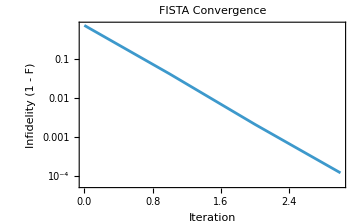

```mathematica
GraphicsGrid[{{PlotOptimalControlWaveform[resDisk,PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"Disk Bound <= 500 Hz"],PlotOptimalControlWaveform[resSmooth,PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"Disk + Power & Smoothness"]},{PlotOptimalControlWaveform[resFista,PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"Slew + TV (FISTA)"],PlotOptimalControlConvergence[resFista,Method->"Infidelity",PlotLabel->"FISTA Convergence"]}},ImageSize->760,Spacings->{20,15}]
```

## 6. Smooth Waveform Parameterizations and Envelopes

Instead of optimizing every slice independently ("PiecewiseConstant"), ControlParameterization projects controls onto a low-dimensional smooth basis â.80.94 such as {"Fourier", n}, {"BSpline", n}, or {"Chebyshev", deg} â.80.94 and ControlWindow applies an envelope (such as "Hann", "Hamming", or "Blackman") so amplitudes start and end cleanly at zero.

```mathematica
resFourier=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",ControlParameterization->{"Fourier",8},ControlWindow->"Hann",RandomSeed->42,TargetFidelity->0.9999];
resBSpline=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",ControlParameterization->{"BSpline",12},ControlWindow->"Hann",RandomSeed->42,TargetFidelity->0.9999];
{"Fourier (8 modes + Hann) Fid"->resFourier["FinalFidelity"],"BSpline (12 knots + Hann) Fid"->resBSpline["FinalFidelity"]}
```

{Fourier (8 modes + Hann) Fid→1.,BSpline (12 knots + Hann) Fid→0.999996}

```mathematica
GraphicsRow[{PlotOptimalControlWaveform[resFourier,PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"Fourier (8 modes) + Hann"],PlotOptimalControlWaveform[resBSpline,PlotLegends->Placed[{"ux","uy"},Above],PlotLabel->"BSpline (12 knots) + Hann"]},ImageSize->760,Spacings->25]
```

-Graphics-

## 7. Optimizers, Warm Restarts, and MultiStart

GRAPEOptimize uses "LBFGS" by default for smooth problems (LBFGSMemory -> 15), and also supports "BFGS", "ConjugateGradient", "SteepestAscent", "FISTA", plus second-order Newton/Trust-Region solvers. You can also warm-start from any previous OptimalControlResult via InitialControls, refine grids from coarse to fine using TimeStepSchedule, or take the best of several initializations with MultiStart.

```mathematica
resCG=GRAPEOptimize[probInv,Optimizer->"ConjugateGradient",MaxIterations->60,RandomSeed->42];
resSA=GRAPEOptimize[probInv,Optimizer->"SteepestAscent",MaxIterations->60,RandomSeed->42];
resSched=GRAPEOptimize[probInv,TimeStepSchedule->{15,40},RandomSeed->42];
resWarm=GRAPEOptimize[H0,ctrls,targetInv,{0.002,40},ControlUnits->"Hz",AmplitudeNormBound->500.,InitialControls->resCG,RandomSeed->42];
resMS=GRAPEOptimize[probInv,MultiStart->3,RandomSeed->100];
TableForm[{{"L-BFGS (default)",resInv["FinalFidelity"],resInv["Iterations"]},{"ConjugateGradient",resCG["FinalFidelity"],resCG["Iterations"]},{"SteepestAscent (60 iters)",resSA["FinalFidelity"],resSA["Iterations"]},{"TimeStepSchedule {15, 40}",resSched["FinalFidelity"],resSched["Iterations"]},{"Warm start + 500 Hz Disk",resWarm["FinalFidelity"],resWarm["Iterations"]},{"MultiStart -> 3",resMS["FinalFidelity"],resMS["Iterations"]}},TableHeadings->{None,{"Strategy","FinalFidelity","Iterations"}}]
```

Strategy | FinalFidelity | Iterations
L-BFGS (default) | 1. | 4
ConjugateGradient | 0.999949 | 4
SteepestAscent (60 iters) | 0.999927 | 3
TimeStepSchedule {15, 40} | 0.999968 | 4
Warm start + 500 Hz Disk | 0.999955 | 2
MultiStart -> 3 | 1. | 4

## 8. Exporting and Using Optimized Pulses

Once optimized, an OptimalControlResult converts directly back into SpinDynamica simulation primitives â.80.94 OptimalControlEventList (for NPropagate / NPropagationOperator / Signal1D / Signal2D), OptimalControlGenerator, OptimalControlPulseSequence, OptimalControlWaveform, and OptimalControlPulseTable â.80.94 as well as spectrometer formats ("Bruker", "SIMPSON", "CSV") via ExportOptimalControlPulse.

```mathematica
evList=OptimalControlEventList[resDisk];
pSeq=OptimalControlPulseSequence[resDisk];
rhoFinal=NPropagate[evList][opI[1,"z"]];
zb=ZeemanBasis[];
mIz=MatrixRepresentation[opI[1,"z"],zb];
mRhoFinal=MatrixRepresentation[rhoFinal,zb];
tbl=OptimalControlPulseTable[resDisk,PhaseUnits->"Degrees",AmplitudeScaling->"Percent"];
{"PulseSequence Head"->Head[pSeq],"NPropagate Final <Iz> (expect -1)"->Re[Tr[mIz.mRhoFinal]/Tr[mIz.mIz]],"PulseTable Slices & Keys"->{tbl["NumSlices"],Keys[tbl]}}
```

{PulseSequence Head→PulseSequence,NPropagate Final <Iz> (expect -1)→-1.,PulseTable Slices & Keys→{40,{NumSlices,TotalDuration,TimeSteps,TimeEdges,TimeMidpoints,UniformTimeStepQ,PhaseUnits,AmplitudeScaling,Channels,Table}}}

```mathematica
{"Bruker JCAMP-DX Preview"->StringTake[ExportOptimalControlPulse[resDisk,"Bruker",Resample->40,Title->"SingleSpin_Inv"],UpTo[200]],"SIMPSON Preview"->StringTake[ExportOptimalControlPulse[resDisk,"SIMPSON",Resample->40],UpTo[140]],"CSV Preview"->StringTake[ExportOptimalControlPulse[resDisk,"CSV",Resample->40],UpTo[140]]}
```

{Bruker JCAMP-DX Preview→##TITLE= SingleSpin_Inv (Ch 1)
##JCAMP-DX= 5.00 Bruker JCAMP library
##DATA TYPE= Shape Data
##ORIGIN= SpinDynamica OptimalControl
##OWNER= SpinDynamica
##MINX= 0.000000
##MAXX= 100.000000
##MINY= 0.0,SIMPSON Preview→337.00297144089905 267.1563495663829
226.25049398085088 193.31445813087083
461.7546434201032 312.47092156488526
293.88208962296017 260.21942,CSV Preview→Slice,TimeStart_s,TimeEnd_s,TimeMid_s,Duration_s,Ch1_Ux_Hz,Ch1_Uy_Hz,Ch1_Amp_Hz,Ch1_Amp_Pct,Ch1_Phase_Deg
1,0.0,0.00004999999999999997,0.000}

## 9. Summary and Quick Reference

A clean single-spin optimal-control workflow consists of four steps:
  1. Build an OptimalControlProblem with explicit units (ControlUnits -> "Hz") and an appropriate target.
  2. Run GRAPEOptimize (starting with default L-BFGS), adding AmplitudeNormBound, smooth penalties, or smooth bases/windows as needed.
  3. Verify the solution independently with VerifyOptimalControlSimulation and inspect waveforms, convergence, and spin trajectories.
  4. Export directly back into SpinDynamica (OptimalControlEventList, OptimalControlPulseSequence) or spectrometer shape formats (ExportOptimalControlPulse).

Symbol / Option | Purpose | Key Notes
OptimalControlProblem[H0, ctrls, tar, t] | Define control problem | Timing {T, n}, T (with TimeSteps), or {dt1, ...}
GRAPEOptimize[prob, opts] | Optimize waveform via GRAPE | Alias OptimalControlOptimize; returns OptimalControlResult
ObservableTarget / StateTarget / UnitaryTarget | Target objective constructors | Use ObservableTarget for traceless NMR spin operators
PhaseFreedom / TargetNormalization | Phase invariance & normalization | "Global" / None; "Frobenius" / "TargetNorm" / "None"
FrequencyUnits / ControlUnits | Drift and RF channel units | "rad/s" (default), "Hz", "kHz", "MHz"
AmplitudeBound / AmplitudeNormBound | Cartesian box / polar disk RF limits | Scalar or per-channel / channel-group specs
PowerPenalty / SmoothnessPenalty | Smooth quadratic regularizers | Suppress RF energy & slice-to-slice ringing
SlewRateBound / L1Penalty / TVPenalty | Rate limits & nonsmooth regularizers | Auto-selects Optimizer -> "FISTA"
ControlParameterization / ControlWindow | Smooth basis & edge envelope | "PiecewiseConstant", {"Fourier", n}, {"BSpline", n}; "Hann"
Optimizer / MultiStart / TimeStepSchedule | Solver & globalization controls | "LBFGS", "ConjugateGradient", "SteepestAscent", "FISTA"
VerifyOptimalControlGradient / Simulation | Accuracy & native SpinDynamica check | Use non-stationary test probe & StepSize ~ 10^-4 for Hz
OptimalControlEventList / PulseSequence / Table | SpinDynamica integration | Feeds directly into NPropagate, Signal1D, Signal2D
ExportOptimalControlPulse | Spectrometer file formatting | "Bruker", "SIMPSON", "CSV" with Resample, Channel, Title
PlotOptimalControlWaveform / Convergence / Trajectory | Visual diagnostics | Cartesian or AmplitudePhase, Infidelity, expectation curves